\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## xAct: xTerior Exterior Calculus

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Load xTras

```mathematica
<<xAct`xTerior`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2015, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.2, {2015,8,23}

CopyRight (C) 2002-2015, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.3, {2015,8,23}

CopyRight (C) 2005-2014, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xTerior`  version 0.9.0, {2015,8,23}

CopyRight (C) 2013, Alfonso Garcia-Parrado Gomez-Lobo and Leo C. Stein, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Hide away ugly dummies

```mathematica
$PrePrint=ScreenDollarIndices;
```

Suppress the “annoying” information.

```mathematica
$DefInfoQ=False;
$UndefInfoQ=False;
$CVVerbose=False;
```

Sometimes we need to know how much time it takes to complete the calculation.

```mathematica
<<xAct`ShowTime1`
$ShowTimeThreshold=0.5
```

0.5

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Setups

Define a Manifold

```mathematica
DefManifold[M3,3,Complement[IndexRange[a,q],{g,h}]]
```

Define a chart

```mathematica
DefChart[cartesian,M3,{1,2,3},{x[],y[],z[]}]
```

```mathematica
Diff[x[]]⋀Diff[y[]]
```

d[x]⋀d[y]

```mathematica
{Diff[x[]],Diff[y[]],Diff[z[]],Diff[x[]]⋀Diff[y[]],Diff[x[]]⋀Diff[z[]],Diff[y[]]⋀Diff[z[]],Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]}
```

{d[x],d[y],d[z],d[x]⋀d[y],d[x]⋀d[z],d[y]⋀d[z],d[x]⋀d[y]⋀d[z]}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Basic Operations

We can represent any differential form, and do operations on it.

```mathematica
ω=(x[]^2+y[]^2)*Diff[z[]]⋀Diff[x[]]-1/(x[]^2+y[]^2)*Diff[x[]]⋀Diff[y[]]
```

-(d[x]⋀d[y])/(x^2+y^2)+d[z]⋀d[x] (x^2+y^2)

```mathematica
ω⋀Diff[z[]]
```

-(d[x]⋀d[y]⋀d[z])/(x^2+y^2)+d[z]⋀d[x]⋀d[z] (x^2+y^2)

```mathematica
%//Simplification
```

-(d[x]⋀d[y]⋀d[z])/(x^2+y^2)

```mathematica
?Simplification
```

Simplification[expr] simplifies expr by calling Simplify[ ToCanonical[expr] ].

The exterior derivative and its properties are implemented by means of the action of  Diff.

```mathematica
ω
```

-(d[x]⋀d[y])/(x^2+y^2)+d[z]⋀d[x] (x^2+y^2)

```mathematica
Diff@ω
%//Simplification
```

2 d[x]⋀d[z]⋀d[x] x+2 d[y]⋀d[z]⋀d[x] y+(2 d[x]⋀d[x]⋀d[y] x+2 d[y]⋀d[x]⋀d[y] y)/((x^2+y^2)^2)

2 d[x]⋀d[y]⋀d[z] y

Define some scalar functions

```mathematica
DefScalarFunction/@{Fx,Fy,Fz};
PrintAs@Fx^="F_x";
PrintAs@Fy^="F_y";
PrintAs@Fz^="F_z";
```

We can use the scalar functions to represent a generic 2-form and do operations on it:

```mathematica
ψ=Fx[x[],y[],z[]]Diff[y[]]⋀Diff[z[]]-Fy[x[],y[],z[]]Diff[x[]]⋀Diff[z[]]+Fz[x[],y[],z[]]Diff[x[]]⋀Diff[y[]]
```

F_z[x,y,z] d[x]⋀d[y]-F_y[x,y,z] d[x]⋀d[z]+F_x[x,y,z] d[y]⋀d[z]

```mathematica
Diff@ψ//Simplification
```

d[x]⋀d[y]⋀d[z] (F_z^(0,0,1)[x,y,z]+F_y^(0,1,0)[x,y,z]+F_x^(1,0,0)[x,y,z])

As is well-known the double exterior derivative is zero.

```mathematica
Diff@Diff@ψ
%//Simplification
```

d[z]⋀d[z]⋀d[y]⋀d[z] F_x^(0,0,2)[x,y,z]-d[z]⋀d[z]⋀d[x]⋀d[z] F_y^(0,0,2)[x,y,z]+d[z]⋀d[z]⋀d[x]⋀d[y] F_z^(0,0,2)[x,y,z]+d[y]⋀d[z]⋀d[y]⋀d[z] F_x^(0,1,1)[x,y,z]+d[z]⋀d[y]⋀d[y]⋀d[z] F_x^(0,1,1)[x,y,z]-d[y]⋀d[z]⋀d[x]⋀d[z] F_y^(0,1,1)[x,y,z]-d[z]⋀d[y]⋀d[x]⋀d[z] F_y^(0,1,1)[x,y,z]+d[y]⋀d[z]⋀d[x]⋀d[y] F_z^(0,1,1)[x,y,z]+d[z]⋀d[y]⋀d[x]⋀d[y] F_z^(0,1,1)[x,y,z]+d[y]⋀d[y]⋀d[y]⋀d[z] F_x^(0,2,0)[x,y,z]-d[y]⋀d[y]⋀d[x]⋀d[z] F_y^(0,2,0)[x,y,z]+d[y]⋀d[y]⋀d[x]⋀d[y] F_z^(0,2,0)[x,y,z]+d[x]⋀d[z]⋀d[y]⋀d[z] F_x^(1,0,1)[x,y,z]+d[z]⋀d[x]⋀d[y]⋀d[z] F_x^(1,0,1)[x,y,z]-d[x]⋀d[z]⋀d[x]⋀d[z] F_y^(1,0,1)[x,y,z]-d[z]⋀d[x]⋀d[x]⋀d[z] F_y^(1,0,1)[x,y,z]+d[x]⋀d[z]⋀d[x]⋀d[y] F_z^(1,0,1)[x,y,z]+d[z]⋀d[x]⋀d[x]⋀d[y] F_z^(1,0,1)[x,y,z]+d[x]⋀d[y]⋀d[y]⋀d[z] F_x^(1,1,0)[x,y,z]+d[y]⋀d[x]⋀d[y]⋀d[z] F_x^(1,1,0)[x,y,z]-d[x]⋀d[y]⋀d[x]⋀d[z] F_y^(1,1,0)[x,y,z]-d[y]⋀d[x]⋀d[x]⋀d[z] F_y^(1,1,0)[x,y,z]+d[x]⋀d[y]⋀d[x]⋀d[y] F_z^(1,1,0)[x,y,z]+d[y]⋀d[x]⋀d[x]⋀d[y] F_z^(1,1,0)[x,y,z]+d[x]⋀d[x]⋀d[y]⋀d[z] F_x^(2,0,0)[x,y,z]-d[x]⋀d[x]⋀d[x]⋀d[z] F_y^(2,0,0)[x,y,z]+d[x]⋀d[x]⋀d[x]⋀d[y] F_z^(2,0,0)[x,y,z]

0

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Find a Potential

Poincaré Lemma
If ω is a p-form and dω = 0 on an open star-shaped set 𝒰 with respect to a point a, then there exists a p-1 form ϕ on 𝒰 such that 
dϕ = ω .

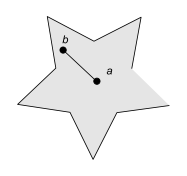

We can attempt to find the form ϕ with the command FindPotential.

```mathematica
?FindPotential
```

FindPotential[form, point, chart] uses the Poincaré lemma to compute a potential for a closed form form (no checks are carried out to ensure that the form is actually closed). The form must be written in some explicit coordinates belonging to chart and the argument point is the point, assumed to be in the same coordinate chart as form, which defines a star-shaped region where the potential is differentiable. A change in the point will give in general a different potential

Any 3-form is closed

```mathematica
η=Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]
```

d[x]⋀d[y]⋀d[z]

A local potential with ℝ^3as the star-shaped set and the origin {0,0,0} as the reference point.

```mathematica
FindPotential[η,{0,0,0},cartesian]
```

1/3 d[y]⋀d[z] x-1/3 d[x]⋀d[z] y+1/3 d[x]⋀d[y] z

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z]

Another potential with another point as the reference

```mathematica
FindPotential[η,{1,1,1},cartesian]//Simplification
```

1/3 (d[y]⋀d[z] (-1+x)-d[x]⋀d[z] (-1+y)+d[x]⋀d[y] (-1+z))

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z]

A more involved example: take the 3-form:

```mathematica
ω2=Diff[x[]]⋀Diff[y[]]⋀Diff[z[]]y[]
```

d[x]⋀d[y]⋀d[z] y

Again it is closed. Let us find a pontential

```mathematica
FindPotential[ω2,{0,0,0},cartesian]
```

1/4 d[y]⋀d[z] x y-1/4 d[x]⋀d[z] y^2+1/4 d[x]⋀d[y] y z

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z] y

```mathematica
FindPotential[ω2,{1,1,1},cartesian]
```

0.640625

1/12 (1+3 y) (d[y]⋀d[z] (-1+x)-d[x]⋀d[z] (-1+y)+d[x]⋀d[y] (-1+z))

```mathematica
Diff@%//Simplification
```

d[x]⋀d[y]⋀d[z] y

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Hodge Dual and Codifferential

If we introduce a metric in a manifold ℳ, then we can define:
Hodge operator  ⋆ : Λ^p(ℳ)→Λ^(n-p)(ℳ)    ExpandHodgeDual
co-differential   δ :  Λ^p(ℳ)→Λ^(p-1)(ℳ)    CodiffToDiff   
                          δ≡(-1)^(n(p+1)+s)⋆ d ⋆

We take a coordinate system predefined in Mathematica.

```mathematica
DefChart[cyl,M3,{1,2,3},{ρ[],θ[],ζ[]}]
(* cyl stands for Cylindrical *)
```

The components of the metric tensor are given by

```mathematica
metricarray=CoordinateChartData["Cylindrical","Metric"][{ρ[],θ[],ζ[]}]
```

{{1,0,0},{0,ρ^2,0},{0,0,1}}

In order that xTerior recognizes this as the metric in cylindrical coordinates one has to wrap it with the CTensor head as follows:

```mathematica
metriccyl=CTensor[metricarray,{-cyl,-cyl}]
```

CTensor[{{1,0,0},{0,ρ^2,0},{0,0,1}},{-cyl,-cyl},0]

```mathematica
SetCMetric[metriccyl,cyl,SignatureOfMetric->{3,0,0}]
```

```mathematica
?SignatureOfMetric
```

SignatureOfMetric[metric] gives the signature of the metric, in the form of a list of three elements: {p1s, m1s, zeros} giving the numbers of +1's, -1's and zeros, respectively, always in this order.

Some calculations

```mathematica
Diff[ρ[]]
```

d[ρ]

```mathematica
expr1=Hodge[metriccyl]@%
```

*[d[ρ]]

Expand Hodge dual

```mathematica
?dx
```

dx[mani] represents a holonomic co-frame in the manifold mani.

```mathematica
ExpandHodgeDual[expr1,dx[M3],metriccyl]
```

dx | 2
 ⋀dx | 3
  √(ρ^2)

```mathematica
%//ToValues
```

d[θ]⋀d[ζ] √(ρ^2)

```mathematica
%//PowerExpand
```

d[θ]⋀d[ζ] ρ

We can use these feature to compute the Hodge Laplacian.

```mathematica
DefScalarFunction[Φ]
```

Forms of degree higher than the dimension will be set to zero automatically.

```mathematica
UseDimensionStart[]
```

```mathematica
?UseDimensionStart
```

UseDimensionStart[] is an instruction that, when issued, makes any expression with degree greater than the manifold dimension equal to zero.

The Hodge laplacian acting on any form Φ is defined by dδ Φ +δ d Φ.

```mathematica
Diff@Codiff[metriccyl]@Φ[ρ[],θ[],ζ[]]+Codiff[metriccyl]@Diff@Φ[ρ[],θ[],ζ[]]
```

d[δ[Φ[ρ,θ,ζ]]]+δ[d[ζ] Φ^(0,0,1)[ρ,θ,ζ]]+δ[d[θ] Φ^(0,1,0)[ρ,θ,ζ]]+δ[d[ρ] Φ^(1,0,0)[ρ,θ,ζ]]

```mathematica
CodiffToDiff@%
```

(*[d[*[d[ζ]]]]) Φ^(0,0,1)[ρ,θ,ζ]+(*[d[ζ]⋀(*[d[ζ]])]) Φ^(0,0,2)[ρ,θ,ζ]+(*[d[*[d[θ]]]]) Φ^(0,1,0)[ρ,θ,ζ]+(*[d[ζ]⋀(*[d[θ]])]) Φ^(0,1,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[d[ζ]])]) Φ^(0,1,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[d[θ]])]) Φ^(0,2,0)[ρ,θ,ζ]+(*[d[*[d[ρ]]]]) Φ^(1,0,0)[ρ,θ,ζ]+(*[d[ζ]⋀(*[d[ρ]])]) Φ^(1,0,1)[ρ,θ,ζ]+(*[d[ρ]⋀(*[d[ζ]])]) Φ^(1,0,1)[ρ,θ,ζ]+(*[d[θ]⋀(*[d[ρ]])]) Φ^(1,1,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[d[θ]])]) Φ^(1,1,0)[ρ,θ,ζ]+(*[d[ρ]⋀(*[d[ρ]])]) Φ^(2,0,0)[ρ,θ,ζ]

We work out the exterior derivative and the Hodge duals

```mathematica
ExpandHodgeDual[%,dx[M3],metriccyl]
```

0.546875

(ρ (*[d[ρ]⋀dx | 1
 ⋀dx | 2
 ]) Φ^(0,0,1)[ρ,θ,ζ])/(√(ρ^2))+√(ρ^2) (*[dx | 3
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(0,0,2)[ρ,θ,ζ]+(ρ (*[d[ρ]⋀dx | 1
 ⋀dx | 3
 ]) Φ^(0,1,0)[ρ,θ,ζ])/((ρ^2)^(3/2))+√(ρ^2) (*[dx | 2
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(0,1,1)[ρ,θ,ζ]-((*[dx | 3
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(0,1,1)[ρ,θ,ζ])/(√(ρ^2))-((*[dx | 2
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(0,2,0)[ρ,θ,ζ])/(√(ρ^2))+(ρ (*[d[ρ]⋀dx | 2
 ⋀dx | 3
 ]) Φ^(1,0,0)[ρ,θ,ζ])/(√(ρ^2))+√(ρ^2) (*[dx | 1
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(1,0,1)[ρ,θ,ζ]+√(ρ^2) (*[dx | 3
 ⋀dx | 2
 ⋀dx | 3
 ]) Φ^(1,0,1)[ρ,θ,ζ]-((*[dx | 1
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(1,1,0)[ρ,θ,ζ])/(√(ρ^2))+√(ρ^2) (*[dx | 2
 ⋀dx | 2
 ⋀dx | 3
 ]) Φ^(1,1,0)[ρ,θ,ζ]+√(ρ^2) (*[dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]) Φ^(2,0,0)[ρ,θ,ζ]

```mathematica
ExpandHodgeDual[%,dx[M3],metriccyl]
```

Φ^(0,0,2)[ρ,θ,ζ]+(Φ^(0,2,0)[ρ,θ,ζ])/ρ^2+(Φ^(1,0,0)[ρ,θ,ζ])/ρ+Φ^(2,0,0)[ρ,θ,ζ]

Compare with Mathematica.

```mathematica
Laplacian[Φ[ρ[],θ[],ζ[]],{ρ[],θ[],ζ[]},"Cylindrical"]//Expand
```

Φ^(0,0,2)[ρ,θ,ζ]+(Φ^(0,2,0)[ρ,θ,ζ])/ρ^2+(Φ^(1,0,0)[ρ,θ,ζ])/ρ+Φ^(2,0,0)[ρ,θ,ζ]

```mathematica
UnsetCMetric@metriccyl
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Example: Hodge Laplacian in the Schwarzschild Metric.

```mathematica
DefManifold[M4,4,{α,β,γ,δ,ν}]
DefChart[sch,M4,{0,1,2,3},{t[],R[],Θ[],λ[]}]
(* sch stands for Schwarzschild *)
```

```mathematica
DefConstantSymbol[mass,PrintAs->"M"]
```

Metric tensor in Matrix form:

```mathematica
metricarray={
{-1+mass/R[],0,0,0},
{0,(1-mass/R[])^(-1),0,0},
{0,0,R[]^2,0},
{0,0,0,R[]^2 Sin[Θ[]]^2}
};
metricarray//MatrixForm
```

(-1+M/R | 0 | 0 | 0
0 | 1/(1-M/R) | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[Θ]^2)

We declare this as a metric tensor.

```mathematica
smetric=CTensor[metricarray,{-sch,-sch}]
```

CTensor[{{-1+M/R,0,0,0},{0,1/(1-M/R),0,0},{0,0,R^2,0},{0,0,0,R^2 Sin[Θ]^2}},{-sch,-sch},0]

```mathematica
SetCMetric[smetric,sch,SignatureOfMetric->{3,1,0}]
```

We use the command UseDimensionStart to get rid of forms whose degree is higher than the dimension of the manifold.

```mathematica
UseDimensionStart[]
```

Computation of the Hodge Laplacian (d δ+δ d)Φ

```mathematica
ScalarsOfChart@sch
```

{t,R,Θ,λ}

```mathematica
?ScalarsOfChart
```

ScalarsOfChart[chart] gives the list of coordinate scalar fields of chart.

```mathematica
Φ@@ScalarsOfChart@sch
```

Φ[t,R,Θ,λ]

```mathematica
Diff@Codiff[smetric][Φ@@ScalarsOfChart@sch]+Codiff[smetric]@Diff[Φ@@ScalarsOfChart@sch]
```

d[δ[Φ[t,R,Θ,λ]]]+δ[d[λ] Φ^(0,0,0,1)[t,R,Θ,λ]]+δ[d[Θ] Φ^(0,0,1,0)[t,R,Θ,λ]]+δ[d[R] Φ^(0,1,0,0)[t,R,Θ,λ]]+δ[d[t] Φ^(1,0,0,0)[t,R,Θ,λ]]

The procedure is similar as before: 
Express the co-differential in terms of exterior derivatives and Hodge duals 
and next we work out the Hodge duals:

```mathematica
CodiffToDiff@%
```

-(*[d[*[d[λ]]]]) Φ^(0,0,0,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[λ]])]) Φ^(0,0,0,2)[t,R,Θ,λ]-(*[d[*[d[Θ]]]]) Φ^(0,0,1,0)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[λ]])]) Φ^(0,0,1,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[Θ]])]) Φ^(0,0,1,1)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[Θ]])]) Φ^(0,0,2,0)[t,R,Θ,λ]-(*[d[*[d[R]]]]) Φ^(0,1,0,0)[t,R,Θ,λ]-(*[d[R]⋀(*[d[λ]])]) Φ^(0,1,0,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[R]])]) Φ^(0,1,0,1)[t,R,Θ,λ]-(*[d[R]⋀(*[d[Θ]])]) Φ^(0,1,1,0)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[R]])]) Φ^(0,1,1,0)[t,R,Θ,λ]-(*[d[R]⋀(*[d[R]])]) Φ^(0,2,0,0)[t,R,Θ,λ]-(*[d[*[d[t]]]]) Φ^(1,0,0,0)[t,R,Θ,λ]-(*[d[t]⋀(*[d[λ]])]) Φ^(1,0,0,1)[t,R,Θ,λ]-(*[d[λ]⋀(*[d[t]])]) Φ^(1,0,0,1)[t,R,Θ,λ]-(*[d[t]⋀(*[d[Θ]])]) Φ^(1,0,1,0)[t,R,Θ,λ]-(*[d[Θ]⋀(*[d[t]])]) Φ^(1,0,1,0)[t,R,Θ,λ]-(*[d[R]⋀(*[d[t]])]) Φ^(1,1,0,0)[t,R,Θ,λ]-(*[d[t]⋀(*[d[R]])]) Φ^(1,1,0,0)[t,R,Θ,λ]-(*[d[t]⋀(*[d[t]])]) Φ^(2,0,0,0)[t,R,Θ,λ]

```mathematica
ExpandHodgeDual[%,dx[M4],smetric]
```

8.375

-(-(2 R (*[d[R]⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ]))/(√(R^4 Sin[Θ]^2))+(R^2 (4 R^3 Sin[Θ]^2 (*[d[R]⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ])+2 Cos[Θ] R^4 Sin[Θ] (*[d[Θ]⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ])))/(2 (R^4 Sin[Θ]^2)^(3/2))) Φ^(0,0,0,1)[t,R,Θ,λ]+(R^2 (*[dx | 3
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(0,0,0,2)[t,R,Θ,λ])/(√(R^4 Sin[Θ]^2))-(-(2 √(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ]))/R^3+(4 R^3 Sin[Θ]^2 (*[d[R]⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ])+2 Cos[Θ] R^4 Sin[Θ] (*[d[Θ]⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ]))/(2 R^2 √(R^4 Sin[Θ]^2))) Φ^(0,0,1,0)[t,R,Θ,λ]+(R^2 (*[dx | 2
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(0,0,1,1)[t,R,Θ,λ])/(√(R^4 Sin[Θ]^2))-(√(R^4 Sin[Θ]^2) (*[dx | 3
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(0,0,1,1)[t,R,Θ,λ])/R^2-(√(R^4 Sin[Θ]^2) (*[dx | 2
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(0,0,2,0)[t,R,Θ,λ])/R^2-(1/2 (-((M-R) √(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/R^2-(√(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/R+((M-R) (4 R^3 Sin[Θ]^2 (*[d[R]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ])+2 Cos[Θ] R^4 Sin[Θ] (*[d[Θ]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ])))/(2 R √(R^4 Sin[Θ]^2)))+1/2 (-(√(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/R+((-M+R) √(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/R^2-((-M+R) (4 R^3 Sin[Θ]^2 (*[d[R]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ])+2 Cos[Θ] R^4 Sin[Θ] (*[d[Θ]⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ])))/(2 R √(R^4 Sin[Θ]^2)))) Φ^(0,1,0,0)[t,R,Θ,λ]+(R^2 (*[dx | 1
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(0,1,0,1)[t,R,Θ,λ])/(√(R^4 Sin[Θ]^2))-(((M-R) √(R^4 Sin[Θ]^2) (*[dx | 3
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)-((-M+R) √(R^4 Sin[Θ]^2) (*[dx | 3
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)) Φ^(0,1,0,1)[t,R,Θ,λ]-(√(R^4 Sin[Θ]^2) (*[dx | 1
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(0,1,1,0)[t,R,Θ,λ])/R^2-(((M-R) √(R^4 Sin[Θ]^2) (*[dx | 2
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)-((-M+R) √(R^4 Sin[Θ]^2) (*[dx | 2
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)) Φ^(0,1,1,0)[t,R,Θ,λ]-(((M-R) √(R^4 Sin[Θ]^2) (*[dx | 1
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)-((-M+R) √(R^4 Sin[Θ]^2) (*[dx | 1
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)) Φ^(0,2,0,0)[t,R,Θ,λ]-(1/2 ((√(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(M-R)+(R √(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(M-R)^2+(R (4 R^3 Sin[Θ]^2 (*[d[R]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ])+2 Cos[Θ] R^4 Sin[Θ] (*[d[Θ]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ])))/(2 (M-R) √(R^4 Sin[Θ]^2)))+1/2 ((R √(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(-M+R)^2-(√(R^4 Sin[Θ]^2) (*[d[R]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(-M+R)-(R (4 R^3 Sin[Θ]^2 (*[d[R]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ])+2 Cos[Θ] R^4 Sin[Θ] (*[d[Θ]⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ])))/(2 (-M+R) √(R^4 Sin[Θ]^2)))) Φ^(1,0,0,0)[t,R,Θ,λ]+(R^2 (*[dx | 0
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ]) Φ^(1,0,0,1)[t,R,Θ,λ])/(√(R^4 Sin[Θ]^2))-((R √(R^4 Sin[Θ]^2) (*[dx | 3
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (M-R))-(R √(R^4 Sin[Θ]^2) (*[dx | 3
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (-M+R))) Φ^(1,0,0,1)[t,R,Θ,λ]-(√(R^4 Sin[Θ]^2) (*[dx | 0
 ⋀dx | 0
 ⋀dx | 1
 ⋀dx | 3
 ]) Φ^(1,0,1,0)[t,R,Θ,λ])/R^2-((R √(R^4 Sin[Θ]^2) (*[dx | 2
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (M-R))-(R √(R^4 Sin[Θ]^2) (*[dx | 2
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (-M+R))) Φ^(1,0,1,0)[t,R,Θ,λ]-(((M-R) √(R^4 Sin[Θ]^2) (*[dx | 0
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)-((-M+R) √(R^4 Sin[Θ]^2) (*[dx | 0
 ⋀dx | 0
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 R)) Φ^(1,1,0,0)[t,R,Θ,λ]-((R √(R^4 Sin[Θ]^2) (*[dx | 1
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (M-R))-(R √(R^4 Sin[Θ]^2) (*[dx | 1
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (-M+R))) Φ^(1,1,0,0)[t,R,Θ,λ]-((R √(R^4 Sin[Θ]^2) (*[dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (M-R))-(R √(R^4 Sin[Θ]^2) (*[dx | 0
 ⋀dx | 1
 ⋀dx | 2
 ⋀dx | 3
 ]))/(2 (-M+R))) Φ^(2,0,0,0)[t,R,Θ,λ]

```mathematica
ExpandHodgeDual[%,dx[M4],smetric]
```

1.6875

(Csc[Θ]^2 Φ^(0,0,0,2)[t,R,Θ,λ])/R^2+(Cot[Θ] Φ^(0,0,1,0)[t,R,Θ,λ])/R^2+(Φ^(0,0,2,0)[t,R,Θ,λ])/R^2-(1/2 ((M-R)/R^2-1/R)+1/2 (-1/R-(-M+R)/R^2)) Φ^(0,1,0,0)[t,R,Θ,λ]-((M-R)/(2 R)-(-M+R)/(2 R)) Φ^(0,2,0,0)[t,R,Θ,λ]-(-R/(2 (M-R))+R/(2 (-M+R))) Φ^(2,0,0,0)[t,R,Θ,λ]

```mathematica
Simplify/@%
```

(Csc[Θ]^2 Φ^(0,0,0,2)[t,R,Θ,λ])/R^2+(Cot[Θ] Φ^(0,0,1,0)[t,R,Θ,λ])/R^2+(Φ^(0,0,2,0)[t,R,Θ,λ])/R^2-((M-2 R) Φ^(0,1,0,0)[t,R,Θ,λ])/R^2-((M-R) Φ^(0,2,0,0)[t,R,Θ,λ])/R+(R Φ^(2,0,0,0)[t,R,Θ,λ])/(M-R)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Tensor Valued Forms

```mathematica
Quit[];
```

```mathematica
<<xAct`xTerior`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2015, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.2, {2015,8,23}

CopyRight (C) 2002-2015, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.3, {2015,8,23}

CopyRight (C) 2005-2014, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xTerior`  version 0.9.0, {2015,8,23}

CopyRight (C) 2013, Alfonso Garcia-Parrado Gomez-Lobo and Leo C. Stein, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
$DefInfoQ=False;
$UndefInfoQ=False;
$CVVerbose=False;
```

```mathematica
DefConstantSymbol@dimension
DefManifold[M,dimension,Complement[IndexRange[a,q],{g,h}]]
```

** DefConstantSymbol: Defining constant symbol dimension.

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

Define a tensor valued form of rank-2 and degree 3

```mathematica
DefDiffForm[ω[-a,-b],M,3,Symmetric[{-a,-b}]]
```

** DefTensor: Defining tensor ω[-a,-b].

We can now construct expressions which involve the wedge product and canonicalize them.

```mathematica
ω[-a,-b]⋀ω[-c,-d]-ω[-d,-c]⋀ω[-b,-a]
```

ω |   |  
a | b⋀ω |   |  
c | d-ω |   |  
d | c⋀ω |   |  
b | a

```mathematica
%//ToCanonical
```

2 ω |   |  
a | b⋀ω |   |  
c | d

```mathematica
UndefDiffForm@ω
```

** UndefTensor: Undefined tensor ω

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Cartan Structure Equations

Def a covariant derivative

```mathematica
DefCovD[CD[-a],{"|","D"},Torsion->True]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

Once we have introduced a covariant derivative we can work with its connection 1 - form and the curvature 2 - form.

```mathematica
ChristoffelForm[CD][a,-b]
%//Deg
```

Γ[D] | a |  
  | b

1

```mathematica
RiemannForm[CD][a,-b]
%//Deg
```

R[D] | a |  
  | b

2

These elements are related by the Cartan structure equations.

```mathematica
CartanStructureEqs={
Diff@Coframe[M][a]==UseCartan[Diff[Coframe[M][a]],CD],Diff@ChristoffelForm[CD][a,-b]==UseCartan[Diff[ChristoffelForm[CD][a,-b]],CD],Diff@TorsionForm[CD][a]==UseCartan[Diff[TorsionForm[CD][a]],CD],Diff@RiemannForm[CD][a,-b]==UseCartan[Diff[RiemannForm[CD][a,-b]],CD]
}
```

{d[θ | a
 ]==-(Γ[D] | a |  
  | b⋀θ | b
 )+𝔗[D] | a
 ,d[Γ[D] | a |  
  | b]==-(Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b)+R[D] | a |  
  | b,d[𝔗[D] | a
 ]==-(Γ[D] | a |  
  | b⋀𝔗[D] | b
 )+θ | b
 ⋀R[D] | a |  
  | b,d[R[D] | a |  
  | b]==Γ[D] | c |  
  | b⋀R[D] | a |  
  | c-R[D] | c |  
  | b⋀Γ[D] | a |  
  | c}

```mathematica
%//ScreenDollarIndices//MatrixForm
```

(d[θ | a
 ]==-(Γ[D] | a |  
  | b⋀θ | b
 )+𝔗[D] | a
 
d[Γ[D] | a |  
  | b]==-(Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b)+R[D] | a |  
  | b
d[𝔗[D] | a
 ]==-(Γ[D] | a |  
  | b⋀𝔗[D] | b
 )+θ | b
 ⋀R[D] | a |  
  | b
d[R[D] | a |  
  | b]==Γ[D] | c |  
  | b⋀R[D] | a |  
  | c-R[D] | c |  
  | b⋀Γ[D] | a |  
  | c)

We can also check the complete integrability conditions of the Cartan system.

```mathematica
Diff/@CartanStructureEqs
```

{0==d[𝔗[D] | a
 ]-d[Γ[D] | a |  
  | b]⋀θ | b
 +Γ[D] | a |  
  | b⋀d[θ | b
 ],0==d[R[D] | a |  
  | b]-d[Γ[D] | a |  
  | c]⋀Γ[D] | c |  
  | b+Γ[D] | a |  
  | c⋀d[Γ[D] | c |  
  | b],0==-(d[Γ[D] | a |  
  | b]⋀𝔗[D] | b
 )+d[θ | b
 ]⋀R[D] | a |  
  | b+Γ[D] | a |  
  | b⋀d[𝔗[D] | b
 ]-θ | b
 ⋀d[R[D] | a |  
  | b],0==d[Γ[D] | c |  
  | b]⋀R[D] | a |  
  | c-d[R[D] | c |  
  | b]⋀Γ[D] | a |  
  | c-Γ[D] | c |  
  | b⋀d[R[D] | a |  
  | c]-R[D] | c |  
  | b⋀d[Γ[D] | a |  
  | c]}

```mathematica
UseCartan[%,CD]
```

{0==θ | b
 ⋀R[D] | a |  
  | b-R[D] | a |  
  | b⋀θ | b
 -Γ[D] | a |  
  | b⋀Γ[D] | b |  
  | c⋀θ | c
 +Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b⋀θ | b
 ,0==Γ[D] | a |  
  | c⋀R[D] | c |  
  | b+Γ[D] | c |  
  | b⋀R[D] | a |  
  | c-R[D] | a |  
  | c⋀Γ[D] | c |  
  | b-R[D] | c |  
  | b⋀Γ[D] | a |  
  | c-Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | d⋀Γ[D] | d |  
  | b+Γ[D] | a |  
  | d⋀Γ[D] | d |  
  | c⋀Γ[D] | c |  
  | b,0==-(R[D] | a |  
  | b⋀𝔗[D] | b
 )+𝔗[D] | b
 ⋀R[D] | a |  
  | b-Γ[D] | a |  
  | b⋀Γ[D] | b |  
  | c⋀𝔗[D] | c
 +Γ[D] | a |  
  | b⋀θ | c
 ⋀R[D] | b |  
  | c+Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b⋀𝔗[D] | b
 -Γ[D] | b |  
  | c⋀θ | c
 ⋀R[D] | a |  
  | b-θ | b
 ⋀Γ[D] | c |  
  | b⋀R[D] | a |  
  | c+θ | b
 ⋀R[D] | c |  
  | b⋀Γ[D] | a |  
  | c,0==-(Γ[D] | c |  
  | b⋀Γ[D] | d |  
  | c⋀R[D] | a |  
  | d)+Γ[D] | c |  
  | b⋀R[D] | d |  
  | c⋀Γ[D] | a |  
  | d-Γ[D] | c |  
  | d⋀Γ[D] | d |  
  | b⋀R[D] | a |  
  | c-Γ[D] | d |  
  | b⋀R[D] | c |  
  | d⋀Γ[D] | a |  
  | c+R[D] | c |  
  | b⋀Γ[D] | a |  
  | d⋀Γ[D] | d |  
  | c+R[D] | d |  
  | b⋀Γ[D] | c |  
  | d⋀Γ[D] | a |  
  | c}

```mathematica
ToCanonical[%]
```

{True,True,True,True}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Example: Einstein-Cartan Theory in 4 - D

We can compute the variational derivative δ_(u^j)ℒ using the command FormVarD.

```mathematica
?FormVarD
```

FormVarD[form,metric][expr] computes the variational derivative of expr, which must be a n-form with n the manifold dimension, with respect to form. In the computation, exterior derivatives are transformed into co-differentials taken with respect of metric.

We set now the manifold dimension to 4 and introduce a metric tensor on it with signature (+1,-1,-1,-1).

```mathematica
dimension=4;
```

```mathematica
DefMetric[{1,3,0},g[-a,-b],gcd,Torsion->True]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative gcd[-a].

** DefTensor: Defining torsion tensor Torsiongcd[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelgcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanngcd[-a,-b,-c,-d]. Antisymmetric pairs cannot be exchanged.

** DefTensor: Defining non-symmetric Ricci tensor Riccigcd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalargcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining non-symmetric Einstein tensor Einsteingcd[-a,-b].

** DefTensor: Defining Weyl tensor Weylgcd[-a,-b,-c,-d]. Antisymmetric pairs cannot be exchanged.

** DefTensor: Defining non-symmetric TFRicci tensor TFRiccigcd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanngcd[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefCovD: Defining covariant derivative LCg[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCg[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCg[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannLCg[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciLCg[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCg[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCg[-a,-b].

** DefTensor: Defining Weyl tensor WeylLCg[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCg[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannLCg[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

In this example we explain how to obtain the basic equations of the Einstein-Cartan theory starting from the Einstein-Hilbert Lagrangian written in terms of differential forms.

```mathematica
RiemannForm[gcd,TangentM][b,-a]⋀Hodge[g][Coframe[M][a]⋀Coframe[M][-b]]
```

R[▽] | b |  
  | a⋀*_g[θ | a
 ⋀θ |  
b]

```mathematica
ℒ=ExpandHodgeDual[%,Coframe[M],g]
```

1/2 ϵg | a |   |   |  
  | b | c | d R[▽] | b |  
  | a⋀θ | c
 ⋀θ | d

We treat θ^j and Γ[▽] | b |  
  | a as independent fields. By definition τ_j≡δ_(θ^j)ℒ is the energy-momentum 3-form, and 𝓈 |   | h
f |  ≡δ_(Γ[▽] | f |  
  | h)ℒ is the intrinsic angular momentum (spin) 3-form.

```mathematica
DefDiffForm[τ[-a],M,3]
```

** DefTensor: Defining tensor τ[-a].

```mathematica
DefDiffForm[𝓈[-a,-b],M,3,Antisymmetric[{-a,-b}]]
```

** DefTensor: Defining tensor 𝓈[-a,-b].

Computation of  τ_j=δ_(θ^j)ℒ

```mathematica
τ[-j]==FormVarD[Coframe[M][j],g]@ℒ
```

τ |  
j==ϵg |   | a |   |  
j |   | b | c θ | b
 ⋀R[▽] |   | c
a |

We perform some manipulations on this expression:

```mathematica
CurvatureFormToTensor[%,Coframe]
```

τ |  
j==-1/2 ϵg |   | a |   |  
j |   | b | c R[▽] |   |   | c |  
d | e |   | a θ | b
 ⋀θ | d
 ⋀θ | e

```mathematica
Hodge[g]/@%
```

*_g[τ |  
j]==-1/2 ϵg |   | a |   |  
j |   | b | c R[▽] |   |   | c |  
d | e |   | a *_g[θ | b
 ⋀θ | d
 ⋀θ | e
 ]

```mathematica
ExpandHodgeDual[%,Coframe[M],g]
```

*_g[τ |  
j]==-1/2 (δ | a |  
  | e δ |   | d
b |   δ |   | c
j |  -δ | a |  
  | e δ |   | c
b |   δ |   | d
j |  +δ |   | d
j |   g | a | c
  |   g |   |  
b | e-δ |   | c
j |   g | a | d
  |   g |   |  
b | e-δ |   | d
b |   g | a | c
  |   g |   |  
j | e+δ |   | c
b |   g | a | d
  |   g |   |  
j | e) R[▽] |   |   | b |  
c | d |   | a θ | e

```mathematica
ToCanonical/@ContractMetric/@%
```

*_g[τ |  
j]==2 R[▽] |   | a
j |   θ |  
a-R[▽] θ |  
j

```mathematica
EinsteinA=%//RicciToEinstein//ContractMetric//Simplification
```

*_g[τ |  
j]==2 G[▽] |   | a
j |   θ |  
a

This is the first part of the Einstein equations "Matter curves the spacetime".

We compute next 𝓈 |   | h
f |  ≡δ_(Γ[▽] | f |  
  | h)ℒ. First write the Lagrangian in terms of the connection 1-form.

```mathematica
CartanStructureEqs[[2]]
```

d[Γ[D] | a |  
  | b]==-(Γ[D] | a |  
  | c⋀Γ[D] | c |  
  | b)+R[D] | a |  
  | b

```mathematica
IndexSolve[CartanStructureEqs[[2]],RiemannForm[CD][a,-b]]
```

{HoldPattern[R[D] | UnderBar[a̲] |  
  | UnderBar[b̲]]:>Module[{c},d[Γ[D] | a |  
  | b]+Γ[D] | a | c
  |  ⋀Γ[D] |   |  
c | b]}

```mathematica
ℒ
```

1/2 ϵg | a |   |   |  
  | b | c | d R[▽] | b |  
  | a⋀θ | c
 ⋀θ | d

```mathematica
ℒ/.(IndexSolve[CartanStructureEqs[[2]],RiemannForm[CD][a,-b]]/.CD->gcd)
```

1/2 ϵg | a |   |   |  
  | b | c | d (d[Γ[▽] | b |  
  | a]⋀θ | c
 ⋀θ | d
 +Γ[▽] | b | e
  |  ⋀Γ[▽] |   |  
e | a⋀θ | c
 ⋀θ | d
 )

Actual variational derivative.

```mathematica
𝓈[-f,l]==FormVarD[ChristoffelForm[gcd][f,-l],g][%]
```

𝓈 |   | l
f |  ==-1/2 ϵg |   | b |   |  
f |   | c | d g | l | a
  |   Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 -1/2 ϵg | l |   |   |  
  | b | c | d g |   |  
f | a Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 -1/2 *_g[δ_g[ϵg |   | l |   |  
f |   | a | b *_g[θ | a
 ⋀θ | b
 ]]]

We simplify the above expression. This is a somewhat long computation.

```mathematica
Hodge[g]/@%
```

*_g[𝓈 |   | l
f |  ]==-1/2 δ_g[ϵg |   | l |   |  
f |   | a | b *_g[θ | a
 ⋀θ | b
 ]]-1/2 ϵg |   | b |   |  
f |   | c | d g | l | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg | l |   |   |  
  | b | c | d g |   |  
f | a *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]

```mathematica
CodiffToDiff/@%
```

*_g[𝓈 |   | l
f |  ]==1/2 (-ϵg |   | l |   |  
f |   | a | b (*_g[d[θ | a
 ]⋀θ | b
 ]-*_g[θ | a
 ⋀d[θ | b
 ]])-*_g[d[ϵg |   | l |   |  
f |   | a | b]⋀θ | a
 ⋀θ | b
 ])-1/2 ϵg |   | b |   |  
f |   | c | d g | l | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg | l |   |   |  
  | b | c | d g |   |  
f | a *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]

```mathematica
%/.MakeRule[{epsilong[-a,-b,-c,-d],epsilong[-a,-b,-c,-d]},MetricOn->All,ContractMetrics->False]
```

*_g[𝓈 |   | l
f |  ]==1/2 (-ϵg |   |   |   |  
f | c | a | b g | l | c
  |   (*_g[d[θ | a
 ]⋀θ | b
 ]-*_g[θ | a
 ⋀d[θ | b
 ]])-g | l | d
  |   *_g[d[ϵg |   |   |   |  
f | d | a | b]⋀θ | a
 ⋀θ | b
 ]-ϵg |   |   |   |  
f | d | a | b *_g[d[g | l | d
  |  ]⋀θ | a
 ⋀θ | b
 ])-1/2 ϵg |   |   |   |  
f | e | c | d g | b | e
  |   g | l | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg |   |   |   |  
e | b | c | d g |   |  
f | a g | l | e
  |   *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]

```mathematica
UseCartan[%,gcd]
```

*_g[𝓈 |   | l
f |  ]==-1/2 ϵg |   |   |   |  
f | e | c | d g | b | e
  |   g | l | a
  |   *_g[Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 ]-1/2 ϵg |   |   |   |  
e | b | c | d g |   |  
f | a g | l | e
  |   *_g[Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 ]+1/2 (-ϵg |   |   |   |  
f | d | a | b g | l | d
  |   *_g[Γ[▽] | j |  
  | j⋀θ | a
 ⋀θ | b
 ]-ϵg |   |   |   |  
f | d | a | b (-*_g[Γ[▽] | d | l
  |  ⋀θ | a
 ⋀θ | b
 ]-*_g[Γ[▽] | l | d
  |  ⋀θ | a
 ⋀θ | b
 ])-ϵg |   |   |   |  
f | c | a | b g | l | c
  |   (-*_g[θ | a
 ⋀𝔗[▽] | b
 ]+*_g[𝔗[▽] | a
 ⋀θ | b
 ]-*_g[Γ[▽] | a |  
  | e⋀θ | e
 ⋀θ | b
 ]+*_g[θ | a
 ⋀Γ[▽] | b |  
  | i⋀θ | i
 ]))

```mathematica
Hodge[g]/@%
```

𝓈 |   | l
f |  ==-1/2 ϵg |   |   |   |  
f | e | c | d g | b | e
  |   g | l | a
  |   Γ[▽] |   |  
a | b⋀θ | c
 ⋀θ | d
 -1/2 ϵg |   |   |   |  
e | b | c | d g |   |  
f | a g | l | e
  |   Γ[▽] | b | a
  |  ⋀θ | c
 ⋀θ | d
 +1/2 (-ϵg |   |   |   |  
f | d | a | b g | l | d
  |   Γ[▽] | j |  
  | j⋀θ | a
 ⋀θ | b
 -ϵg |   |   |   |  
f | d | a | b (-(Γ[▽] | d | l
  |  ⋀θ | a
 ⋀θ | b
 )-Γ[▽] | l | d
  |  ⋀θ | a
 ⋀θ | b
 )-ϵg |   |   |   |  
f | c | a | b g | l | c
  |   (-(θ | a
 ⋀𝔗[▽] | b
 )+𝔗[▽] | a
 ⋀θ | b
 -Γ[▽] | a |  
  | e⋀θ | e
 ⋀θ | b
 +θ | a
 ⋀Γ[▽] | b |  
  | i⋀θ | i
 ))

```mathematica
ContractMetric/@%
```

𝓈 |   | l
f |  ==1/2 ϵg |   | l |   |  
f |   | a | b θ | a
 ⋀𝔗[▽] | b
 -1/2 ϵg |   | l |   |  
f |   | a | b 𝔗[▽] | a
 ⋀θ | b
 +1/2 ϵg |   | l |   |  
f |   | a | b Γ[▽] | a |  
  | c⋀θ | c
 ⋀θ | b
 -1/2 ϵg | l |   |   |  
  | a | b | c Γ[▽] | a |  
  | f⋀θ | b
 ⋀θ | c
 -1/2 ϵg |   | l |   |  
f |   | a | b Γ[▽] | c |  
  | c⋀θ | a
 ⋀θ | b
 +1/2 ϵg |   |   |   |  
f | c | a | b Γ[▽] | c | l
  |  ⋀θ | a
 ⋀θ | b
 -1/2 ϵg |   | a |   |  
f |   | b | c Γ[▽] | l |  
  | a⋀θ | b
 ⋀θ | c
 +1/2 ϵg |   |   |   |  
f | c | a | b Γ[▽] | l | c
  |  ⋀θ | a
 ⋀θ | b
 -1/2 ϵg |   | l |   |  
f |   | a | b θ | a
 ⋀Γ[▽] | b |  
  | c⋀θ | c

```mathematica
ToCanonical/@%
```

𝓈 |   | l
f |  ==ϵg |   | l | a | b
f |   |   |   θ |  
a⋀𝔗[▽] |  
b-ϵg |   | l | a | b
f |   |   |   Γ[▽] |   | c
a |  ⋀θ |  
b⋀θ |  
c-1/2 ϵg | l | a | b | c
  |   |   |   Γ[▽] |   |  
a | f⋀θ |  
b⋀θ |  
c+1/2 ϵg |   | a | b | c
f |   |   |   Γ[▽] |   | l
a |  ⋀θ |  
b⋀θ |  
c-1/2 ϵg |   | l | a | b
f |   |   |   Γ[▽] | c |  
  | c⋀θ |  
a⋀θ |  
b

```mathematica
%/.l->-l
```

𝓈 |   |  
f | l==ϵg |   |   | a | b
f | l |   |   θ |  
a⋀𝔗[▽] |  
b-ϵg |   |   | a | b
f | l |   |   Γ[▽] |   | c
a |  ⋀θ |  
b⋀θ |  
c-1/2 ϵg |   | a | b | c
l |   |   |   Γ[▽] |   |  
a | f⋀θ |  
b⋀θ |  
c+1/2 ϵg |   | a | b | c
f |   |   |   Γ[▽] |   |  
a | l⋀θ |  
b⋀θ |  
c-1/2 ϵg |   |   | a | b
f | l |   |   Γ[▽] | c |  
  | c⋀θ |  
a⋀θ |  
b

```mathematica
ConnectionFormToTensor[%,PD,Coframe]
```

𝓈 |   |  
f | l==ϵg |   |   | a | b
f | l |   |   θ |  
a⋀𝔗[▽] |  
b-1/2 Γ[▽] | c |   |  
  | d | c ϵg |   |   | a | b
f | l |   |   θ | d
 ⋀θ |  
a⋀θ |  
b+1/2 Γ[▽] |   |   |  
a | d | l ϵg |   | a | b | c
f |   |   |   θ | d
 ⋀θ |  
b⋀θ |  
c-Γ[▽] |   |   | c
a | d |   ϵg |   |   | a | b
f | l |   |   θ | d
 ⋀θ |  
b⋀θ |  
c-1/2 Γ[▽] |   |   |  
a | d | f ϵg |   | a | b | c
l |   |   |   θ | d
 ⋀θ |  
b⋀θ |  
c

```mathematica
Hodge[g]/@%
```

*_g[𝓈 |   |  
f | l]==ϵg |   |   | a | b
f | l |   |   *_g[θ |  
a⋀𝔗[▽] |  
b]-1/2 Γ[▽] | c |   |  
  | d | c ϵg |   |   | a | b
f | l |   |   *_g[θ | d
 ⋀θ |  
a⋀θ |  
b]+1/2 Γ[▽] |   |   |  
a | d | l ϵg |   | a | b | c
f |   |   |   *_g[θ | d
 ⋀θ |  
b⋀θ |  
c]-Γ[▽] |   |   | c
a | d |   ϵg |   |   | a | b
f | l |   |   *_g[θ | d
 ⋀θ |  
b⋀θ |  
c]-1/2 Γ[▽] |   |   |  
a | d | f ϵg |   | a | b | c
l |   |   |   *_g[θ | d
 ⋀θ |  
b⋀θ |  
c]

```mathematica
ExpandHodgeDual[#,Coframe[M],g]&/@%
```

*_g[𝓈 |   |  
f | l]==-Γ[▽] |   |   |  
a | b | l (δ | a |  
  | c δ |   | b
f |  -g | a | b
  |   g |   |  
f | c) θ | c
 +Γ[▽] | a |   |  
  | b | a (-δ |   | b
l |   g |   |  
f | c+δ |   | b
f |   g |   |  
l | c) θ | c
 +Γ[▽] |   |   |  
a | b | f (δ | a |  
  | c δ |   | b
l |  -g | a | b
  |   g |   |  
l | c) θ | c
 -Γ[▽] |   |   | b
a | c |   (δ | a |  
  | d δ |   | c
l |   g |   |  
f | b-δ | a |  
  | b δ |   | c
l |   g |   |  
f | d-δ | a |  
  | d δ |   | c
f |   g |   |  
l | b+g | a | c
  |   g |   |  
f | d g |   |  
l | b+δ | a |  
  | b δ |   | c
f |   g |   |  
l | d-g | a | c
  |   g |   |  
f | b g |   |  
l | d) θ | d
 +ϵg |   |   | a | b
f | l |   |   *_g[θ |  
a⋀𝔗[▽] |  
b]

```mathematica
%//ContractMetric//ToCanonical
```

*_g[𝓈 |   |  
f | l]==ϵg |   |   | a | b
f | l |   |   *_g[θ |  
a⋀𝔗[▽] |  
b]

```mathematica
Hodge[g]/@%
```

𝓈 |   |  
f | l==ϵg |   |   | a | b
f | l |   |   θ |  
a⋀𝔗[▽] |  
b

This is the second set of Einstein equations (intrinsic spin generates torsion).

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## References and Further Reading Material

xTerior’s official manual: xTeriorDoc.nb

xTeriorSlideShowYT.nb